# Shapes III

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Column@Table[ToString@i<>".  ",{i,21}];
```

```mathematica
niceForm[{x_,y_}]:=TraditionalForm[x î + y ĵ]
niceForm[{x_,y_,z_}] := TraditionalForm[x î + y ĵ+z k̂]
```

```mathematica
ihat:={0,1}; ihat3:={1,0,0};
jhat:={1,0}; jhat3:={0,1,0};
khat3:={0,0,1};
```

```mathematica
myRegionPlot[f_,bounds_]:=RegionPlot[f,{x,bounds[[1]],bounds[[2]]},{y,bounds[[1]],bounds[[2]]},PlotPoints->60]
myRegionPlot[f_] := (bounds=RegionBounds[ImplicitRegion[f,{x,y}]];min=Min[bounds[[1]][[1]],bounds[[2]][[1]]];max=Max[bounds[[1]][[2]],bounds[[2]][[2]]];myRegionPlot[f,{min,max}])
```

```mathematica
regionIntegrate[region_,function_]:=Integrate[function,{x,y}∈ImplicitRegion[region,{x,y}]]
regionIntegrate[region_]:=regionIntegrate[region,1]
```

## 1: circle

```mathematica
Begin["One`"]
```

One`

Defining r[u]

```mathematica
r[θ_]:={R Sin[θ]+Subscript[x, 0],R Cos[θ]+Subscript[y, 0]}
```

Tangent vector

```mathematica
t[u_]:=r'[u]/Norm[r'[u]];
TraditionalForm@FullSimplify[t[u],{R>0,u∈Reals}]
```

{cos(u),-sin(u)}

Normal vector

```mathematica
n[u_]:=t'[u]/Norm[t'[u]]
TraditionalForm@FullSimplify[n[u],{R>0,u∈Reals}]
```

{-sin(u),-cos(u)}

Visualization

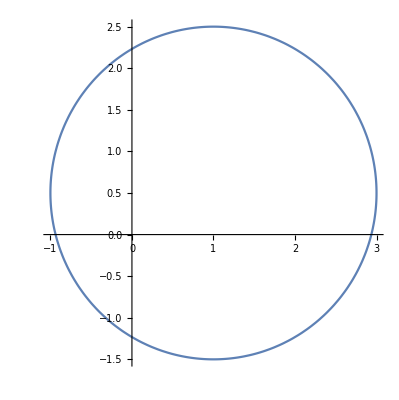

```mathematica
ParametricPlot[r[θ]/.{Subscript[x, 0]->1,Subscript[y, 0]->.5,R->2},{θ,0,2 π}]
```

Curve length

```mathematica
l=FullSimplify[Integrate[Norm[r'[u]],{u,0,2 π}],{R>0}]
```

2 π R

```mathematica
End[]
```

One`

## 2: ellipse

```mathematica
Begin["Two`"]
```

Two`

Defining r[u]

```mathematica
r[θ_]:={a Sin[θ]+Subscript[x, 0],b Cos[θ]+Subscript[y, 0]}
```

Tangent vector

```mathematica
t[u_]:=r'[u]/Norm[r'[u]];
TraditionalForm@FullSimplify[t[u],{a>b>0,u∈Reals}]
```

{(a cos(u))/(√(Abs[a cos(u)]^2+Abs[b sin(u)]^2)),-(b sin(u))/(√(Abs[a cos(u)]^2+Abs[b sin(u)]^2))}

Normal vector

```mathematica
n[u_]:=t'[u]/Norm[t'[u]]
TraditionalForm@FullSimplify[n[u],{a>b>0,u∈Reals}]
```

{-(b sin(u))/(√(a^2 cos^2(u)+b^2 sin^2(u))),-(a cos(u))/(√(a^2 cos^2(u)+b^2 sin^2(u)))}

Visualization

```mathematica
case={Subscript[x, 0]->1,Subscript[y, 0]->.5,a->2,b->1.5};
```

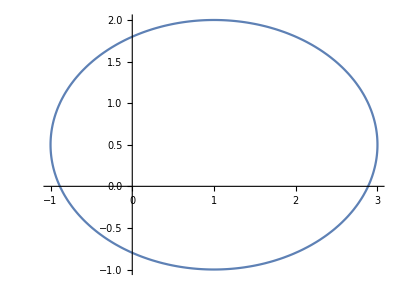

```mathematica
ParametricPlot[r[θ]/.case,{θ,0,2 π}]
```

Curve length

```mathematica
l=FullSimplify[Integrate[Norm[r'[u]]/.case,{u,0,2 π}],{a>b>0}]
```

11.0517

```mathematica
End[]
```

Two`

## 3: spiral

### Visualization

```mathematica
Begin["Three`"]
```

Three`

Defining r[u]

```mathematica
r[u_]:={a E^(b u) Cos[u],a E^(b u) Sin[u]}
$Assumptions={a>0,b<0,u≥0};
```

Tangent vector

```mathematica
t[u_]:=r'[u]/Norm[r'[u]];
TraditionalForm@FullSimplify[t[u]]
```

{(b cos(u)-sin(u))/(√(b^2+1)),(b sin(u)+cos(u))/(√(b^2+1))}

Normal vector

```mathematica
n[u_]:=t'[u]/Norm[t'[u]]/.case
(*TraditionalForm@Simplify[n[u]]*)
```

Visualization

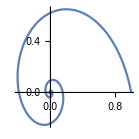

```mathematica
case={a->1,b->-.3};
ParametricPlot[r[θ]/.case,{θ,0,100},PlotRange->All]
```

### Analysis

The parameter a seems to control the x-intercept of the starting point, while b controls how quickly the spiral converges.

Curve length

```mathematica
l=Integrate[Norm[r'[u]]/.case,{u,0,∞}]
```

3.4801

```mathematica
End[]
```

Three`

## 4: 3D spiral

### Setup

```mathematica
Begin["Four`"]
```

Four`

Defining r[u]

```mathematica
r[u_]:={a  Cos[u],a  Sin[u],b u}
$Assumptions={a>0,b>0,u≥0};
```

Tangent vector

```mathematica
t[u_]:=r'[u]/Norm[r'[u]];
TraditionalForm@FullSimplify[t[u]]
```

{-(a sin(u))/(√(a^2+b^2)),(a cos(u))/(√(a^2+b^2)),b/(√(a^2+b^2))}

Normal vector

Note that the normal vector shown here is actually one of many possible normal vectors. In 2d, it was one of the two perpendicular vectors available, but in 3D, a whole plane of perpendicular vectors are available.

```mathematica
n[u_]:=t'[u]/Norm[t'[u]]/.case
TraditionalForm@FullSimplify[n[u]]
```

{-1. cos(u),-1. sin(u),0.}

### Visualization

```mathematica
case={a->1,b->-.3};
ParametricPlot3D[r[θ]/.case,{θ,0,10 π},PlotRange->All]
```

-Graphics3D-

### Analysis

The parameter a seems to control the x-intercept of the starting point, while b controls how quickly the spiral converges.

Curve length

```mathematica
l=Integrate[Norm[r'[u]],{u,0,10π}]
l/.case
```

10 √(a^2+b^2) π

32.7992

```mathematica
End[]
```

Four`

## 5: Boat hull

### Setup

```mathematica
Begin["Five`"]
```

Five`

Defining r[u]

```mathematica
r[u_]:={u,Abs[u]^n-1}
$Assumptions={n>0,-1<u<1};
```

Tangent vector

```mathematica
t[u_]:=FullSimplify@Normalize[r'[u]];
TraditionalForm@FullSimplify[t[u]]
FullSimplify[%,u>0]
```

{1/(√(n^2 (u^2)^(n-1)+1)),(n sgn(u) Abs[u]^n)/(√(n^2 (u^2)^n (sgn(u))^2+u^2))}

{1/(√(1+n^2 u^(-2+2 n))),(n u^n)/(√(u^2+n^2 u^(2 n)))}

Normal vector

```mathematica
norm[u_]:=Normalize[t'[u]]/.n->2
TraditionalForm@FullSimplify[norm[u]]
FullSimplify[%,u>0]
```

{-(2 u (sgn(u))^3 (u Abs''(u)+sgn(u)))/(√(4 u^2+1) Abs[(sgn(u))^2+Abs[u] Abs''(u)]),(sgn(u Abs''(u)+(sgn(u))^3))/(√(4 u^2+1) sgn(u))}

{-(2 u Sign[1+u Abs''[u]])/(√(1+4 u^2)),Sign[1+u Abs''[u]]/(√(1+4 u^2))}

### Visualization

```mathematica
Manipulate[case={n->i};
ParametricPlot[r[u]/.case,{u,-1,1},PlotRange->All],{i,1,10}]
```

### Analysis

Curve length

```mathematica
Manipulate[case={n->i};
2*Integrate[Norm[r'[u]]/.case,{u,0,1}],{i,1,10}]
```

```mathematica
l=Integrate[Norm[r'[u]]/.case,{u,0,10π}]
l/.case
```

10 √(a^2+b^2) π

32.7992

### Underwater Hull

```mathematica
End[]
```

Four`

## 6: Linear Bézier

```mathematica
Begin["Six`"]
```

Seven`

#### Setup

```mathematica
r[u_]:=(1-u)pts[[1]]+u pts[[2]]
$Assumptions={u∈Reals};
```

#### Plotting

pts→{{1,4},{3,5}}

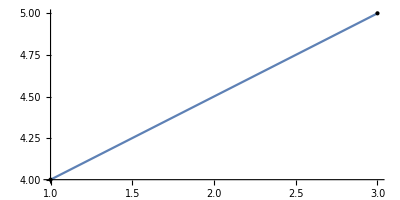

```mathematica
case=pts->{{1,4},{3,5}}
Show[ParametricPlot[r[u]/.case,{u,0,1}],Graphics@Point[pts/.case]]
```

```mathematica
End[]
```

Seven`

## 7: Quadratic Bézier

```mathematica
Begin["Seven`"]
```

Eight`

#### Setup

```mathematica
r[u_]:=(1−u)^2 pts[[1]]+2u (1−u) pts[[2]]+u^2 pts[[3]]
$Assumptions={u∈Reals};
```

#### Plotting

Part::partd: Part specification pts⟦1⟧ is longer than depth of object.

Part::partd: Part specification pts⟦2⟧ is longer than depth of object.

Part::partd: Part specification pts⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

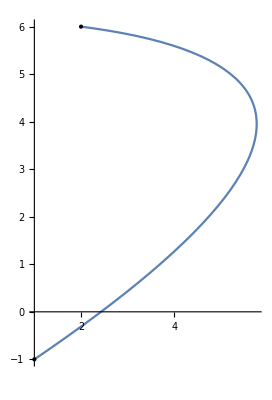

```mathematica
case=pts->{{2,6},{10,5},{1,-1}};
Show[ParametricPlot[r[u]/.case,{u,0,1}],Graphics@Point[pts/.case]]
```

```mathematica
End[]
```

Eight`

## 8: Cubic Bézier

```mathematica
Begin["Eight`"]
```

Nine`

#### Setup

```mathematica
r[u_]:=(1−u)^3 pts[[1]]+3u (1−u)^2 pts[[2]]+3u^2 (1−u) pts[[3]]+u^3 pts[[4]]
$Assumptions={u∈Reals};
```

#### Plotting

pts→{{0,6},{3,5},{1,-1},{0,10}}

Part::partd: Part specification pts⟦1⟧ is longer than depth of object.

Part::partd: Part specification pts⟦2⟧ is longer than depth of object.

Part::partd: Part specification pts⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

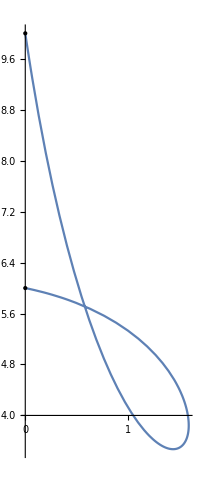

```mathematica
case=pts->{{0,6},{3,5},{1,-1},{0,10}}
Show[ParametricPlot[r[u]/.case,{u,0,1}],Graphics@Point[pts/.case]]
```

```mathematica
End[]
```

Nine`

## 9: Donut

```mathematica
Begin["Nine`"]
```

Nine`

#### Setup

```mathematica
r[u_,v_]:=(a+radius Cos[u]) Cos[v] ihat3+(a+radius Cos[u])Sin[v] jhat3+radius Sin[u] khat3
$Assumptions={radius<a,u∈Reals,v∈Reals,radius>0}
```

{radius<a,u∈Reals,v∈Reals,radius>0}

#### Plotting

```mathematica
case={radius->6,a->14}
ParametricPlot3D[r[u,v]/.case,{u,0,2π},{v,0,2π}]
```

{radius→6,a→14}

-Graphics3D-

#### Normal Vector

```mathematica
norm=FullSimplify@Normalize[D[r[u,v],u]×D[r[u,v],v]];
niceForm[norm]
```

î (-cos(u)) cos(v)-ĵ cos(u) sin(v)-k̂ sin(u)

#### Surface Area

```mathematica
TraditionalForm@Integrate[Norm[D[r[u,v],u]×D[r[u,v],v]],{u,0,2π},{v,0,2π}]
```

4 π^2 a radius

```mathematica
End[]
```

Nine`

## 10: Spray

```mathematica
Begin["Ten`"]
```

Ten`

#### Setup

```mathematica
x=(u L)/2;
z=v ((16 H x^4)/L^4-H);
y=(4 W x^2)/(2 L^2)-1/2 W √((H+z)/H);
r[u_,v_]:={x,y,z}
$Assumptions={H>0,L>0,W>0,u∈Reals,v∈Reals}
```

{H>0,L>0,W>0,u∈Reals,v∈Reals}

#### Plotting

```mathematica
case={H->3,W->6,L->10}
ParametricPlot3D[r[u,v]/.case,{u,-1,1},{v,0,1}]
```

{H→3,W→6,L→10}

-Graphics3D-

#### Normal Vector

```mathematica
norm=FullSimplify@Normalize[D[r[u,v],u]×D[r[u,v],v]];
TraditionalForm[norm]
```

{(8 H u (u^4-1) W)/(Abs[u^4-1] √((L^2 W^2)/Abs[(u^4-1) v+1]+16 H^2 (L^2+4 u^2 W^2))),-(4 H L (u^4-1))/(Abs[u^4-1] √((L^2 W^2)/Abs[(u^4-1) v+1]+16 H^2 (L^2+4 u^2 W^2))),-(L (u^4-1) W)/(Abs[u^4-1] √(((u^4-1) v+1) ((L^2 W^2)/Abs[(u^4-1) v+1]+16 H^2 (L^2+4 u^2 W^2))))}

#### Surface Area

```mathematica
integrand=FullSimplify@Norm[D[r[u,v],u]×D[r[u,v],v]]/.case;
result=Integrate[integrand,{u,-1,1},{v,0,1}]
N@result
```

∫_-1^1 -1/(8 √(25+36 u^2))3 (-4 √(3125+8100 u^2+5184 u^4)+4 u^2 √((25+36 u^2) (25+100 u^4+144 u^6))-25 Log[225+288 u^2+4 √(3125+8100 u^2+5184 u^4)]+25 Log[25+4 u^2 (50 u^2+72 u^4+√((25+36 u^2) (25+100 u^4+144 u^6)))])ⅆu

35.1718

```mathematica
End[]
```

Ten`

## 11: Bezier Surfaces

Warning: This section doesn’t work. It is included here only for completeness.

```mathematica
Begin["Eleven`"]
```

Eleven`

```mathematica
CellPrint@ImportString["$B_i^n(u) = \\frac{n!}{i!(n-i)!} u^i (1-u)^{n-i}$","LaTeX"][[1]]
```

```mathematica
B[i_,n_,u_] := Expand[
  (n!/(i!*(n - i)!))*u^i*
   (1 - u)^(n - i)]
```

```mathematica
B[1,2,3]
```

-12

```mathematica
r[u_,v_]:=Sum[B[i,n,u]B[j,m,v] pts[[i+1,j+1]],{j,0,m},{i,0,n}]
```

```mathematica
case={n->1,m->1,pts->{{{0,0,0},{1,1,1}},{{2,2,2},{3,3,3}}}};
Show[ParametricPlot3D[r[u,v,pts/.case]/.case,{u,0,1},{v,0,1},PlotPoints->5,MaxRecursion->1](*,Graphics3D@Point[pts/.case]*)]
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification {{{0,0,0},{1,1,1}},{{2,2,2},{3,3,3}}}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{{0.,0.,0.},{1.,1.,1.}},{{2.,2.,2.},{3.,3.,3.}}}⟦0,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics3D-

```mathematica
B[1,3,u]
```

3 u-6 u^2+3 u^3

```mathematica
r[.2,.7]/.case
```

Part::pkspec1: The expression 1+i cannot be used as a part specification.

{1.1,1.1}

```mathematica
Sum[{0,1,4,7}[[i+1]],{i,1,3}]
```

12

```mathematica
End[]
```

Eleven`